## Вариант 4, Крюк В.В.

### Задание 1

```mathematica
f[x_]=(4 x^2-5x+1)/(√(2+x^2+√((2+x^2)^5)));
```

### n=6

```mathematica
a=0;
b=6;
n=6;
h=(b-a)/n;
data=N[Table[{a+i h,f[a+i h]},{i,0,n}]]
```

{{0.,0.361389},{1.,0.},{2.,0.721298},{3.,1.08345},{4.,1.20586},{5.,1.23046},{6.,1.21631}}

```mathematica
TableForm[data]
```

0. | 0.361389
1. | 0.
2. | 0.721298
3. | 1.08345
4. | 1.20586
5. | 1.23046
6. | 1.21631

```mathematica
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
```

### а)

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*Product[If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1],{j,1,Length[dataX]}];
Ln=LagrangeInterpolation[data[[All,1]],data[[All,2]],n+1]//Simplify
```

0.361389-2.32027 x+3.16438 x^2-1.5273 x^3+0.362481 x^4-0.0426823 x^5+0.00199066 x^6

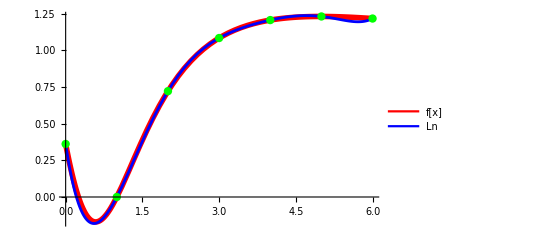

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

### б)

```mathematica
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=""]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=diff[i+1,k-1]-diff[i,k-1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
TableForm[tab]
```

0.361389 | -0.361389 | 1.08269 | -1.44183 | 1.56123 | -1.53869 | 1.43328
0. | 0.721298 | -0.359144 | 0.119397 | 0.0225395 | -0.105414 | 
0.721298 | 0.362154 | -0.239747 | 0.141937 | -0.0828744 |  | 
1.08345 | 0.122407 | -0.09781 | 0.0590624 |  |  | 
1.20586 | 0.0245974 | -0.0387476 |  |  |  | 
1.23046 | -0.0141501 |  |  |  |  | 
1.21631 |  |  |  |  |  |

### в)

```mathematica
findNewtonInter[dataX_,dataY_,deltaTab_,h_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-dataX[[n]])/h+k-1))/Factorial[i]*deltaTab[[n-i,i+1]]);
Pn=findNewtonInter[dataX,dataY,tab,h,n+1]//Simplify
```

0.361389-2.32027 x+3.16438 x^2-1.5273 x^3+0.362481 x^4-0.0426823 x^5+0.00199066 x^6

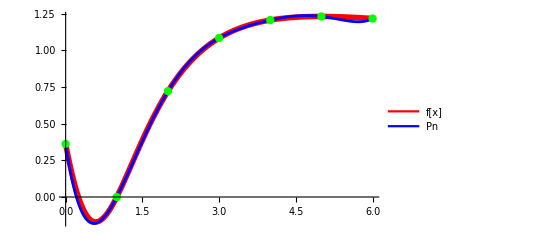

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

### г)

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np]
```

0.361389-2.32027 x+3.16438 x^2-1.5273 x^3+0.362481 x^4-0.0426823 x^5+0.00199066 x^6

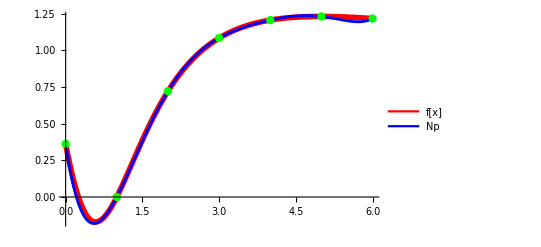

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

### д)

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Np/.x->2.4316
```

0.920893

0.926478

0.926478

0.926478

### e)

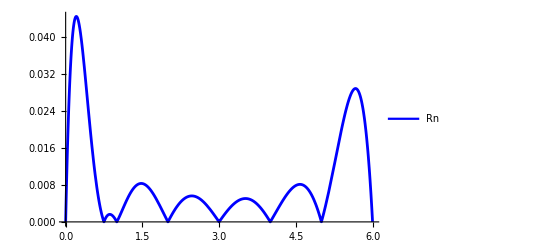

```mathematica
Rn=Abs[f[x]-Np];
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
Maximize[{Rn,a<=x<=b},x]
```

{0.044415,{x→0.208523}}

```mathematica
ClearAll
```

ClearAll

### n=10

```mathematica
a=0;
b=6;
n=10;
h=(b-a)/n;
data=N[Table[{a+i h,f[a+i h]},{i,0,n}]]
```

{{0.,0.361389},{0.6,-0.169493},{1.2,0.150834},{1.8,0.601076},{2.4,0.908823},{3.,1.08345},{3.6,1.17407},{4.2,1.2159},{4.8,1.2298},{5.4,1.22766},{6.,1.21631}}

```mathematica
TableForm[data]
```

0. | 0.361389
0.6 | -0.169493
1.2 | 0.150834
1.8 | 0.601076
2.4 | 0.908823
3. | 1.08345
3.6 | 1.17407
4.2 | 1.2159
4.8 | 1.2298
5.4 | 1.22766
6. | 1.21631

```mathematica
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
```

### a)

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*Product[If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1],{j,1,Length[dataX]}];
Ln=LagrangeInterpolation[data[[All,1]],data[[All,2]],n+1]//Simplify
```

0.361389-1.8914 x+1.4246 x^2+1.33727 x^3-2.15145 x^4+1.26835 x^5-0.424881 x^6+0.0878129 x^7-0.0111179 x^8+0.000792822 x^9-0.0000244297 x^10

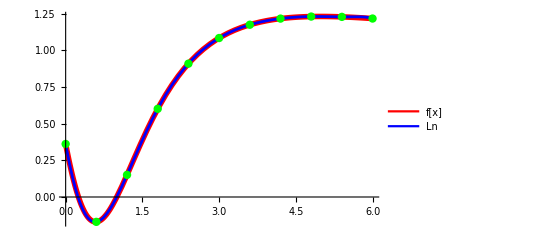

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

### б)

```mathematica
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=""]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=diff[i+1,k-1]-diff[i,k-1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
TableForm[tab]
```

0.361389 | -0.530882 | 0.851209 | -0.721294 | 0.448885 | -0.167098 | -0.074962 | 0.26343 | -0.398841 | 0.487186 | -0.536035
-0.169493 | 0.320327 | 0.129915 | -0.27241 | 0.281787 | -0.24206 | 0.188468 | -0.135411 | 0.0883454 | -0.0488492 | 
0.150834 | 0.450242 | -0.142495 | 0.00937676 | 0.0397266 | -0.053592 | 0.0530574 | -0.0470653 | 0.0394962 |  | 
0.601076 | 0.307747 | -0.133118 | 0.0491034 | -0.0138653 | -0.000534612 | 0.00599209 | -0.00756912 |  |  | 
0.908823 | 0.174629 | -0.0840147 | 0.0352381 | -0.0144 | 0.00545747 | -0.00157703 |  |  |  | 
1.08345 | 0.0906145 | -0.0487767 | 0.0208381 | -0.00894248 | 0.00388044 |  |  |  |  | 
1.17407 | 0.0418378 | -0.0279386 | 0.0118956 | -0.00506204 |  |  |  |  |  | 
1.2159 | 0.0138992 | -0.016043 | 0.00683358 |  |  |  |  |  |  | 
1.2298 | -0.00214371 | -0.00920938 |  |  |  |  |  |  |  | 
1.22766 | -0.0113531 |  |  |  |  |  |  |  |  | 
1.21631 |  |  |  |  |  |  |  |  |  |

### в)

```mathematica
findNewtonInter[dataX_,dataY_,deltaTab_,h_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-dataX[[n]])/h+k-1))/Factorial[i]*deltaTab[[n-i,i+1]]);
Pn=findNewtonInter[dataX,dataY,tab,h,n+1]//Simplify
```

0.361389-1.8914 x+1.4246 x^2+1.33727 x^3-2.15145 x^4+1.26835 x^5-0.424881 x^6+0.0878129 x^7-0.0111179 x^8+0.000792822 x^9-0.0000244297 x^10

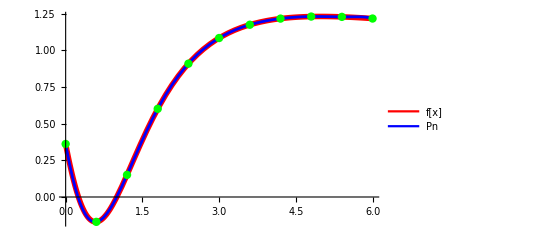

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

### г)

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np]
```

0.361389-1.8914 x+1.4246 x^2+1.33727 x^3-2.15145 x^4+1.26835 x^5-0.424881 x^6+0.0878129 x^7-0.0111179 x^8+0.000792822 x^9-0.0000244297 x^10

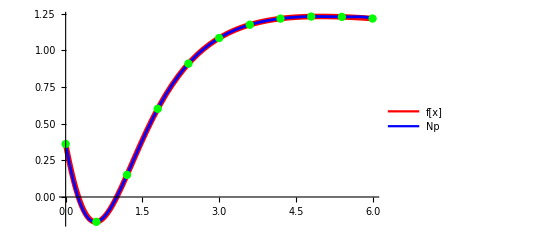

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

### д)

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Np/.x->2.4316
```

0.920893

0.920865

0.920865

0.920865

### e)

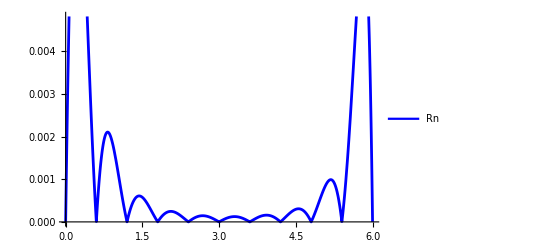

```mathematica
Rn=Abs[f[x]-Np];
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
Maximize[{Rn,a<=x<=b},x]
```

{0.00894544,{x→0.217494}}

### ж) Увеличение количества узлов интерполяции привело к снижению погрешности интерполяции, что демонстрирует влияние числа узлов на точность интерполирования

## Задание 2

### n = 6

```mathematica
n=6;
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i];]
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
TableForm[data]
```

5.92478 | 1.21808
5.34549 | 1.22831
4.30165 | 1.21981
3. | 1.08345
1.69835 | 0.533034
0.654506 | -0.164007
0.0752163 | 0.232961

### а)

```mathematica
findDividedDiff[dataX_,dataY_,first_,last_]:=If[first+1==last,(dataY[[last]]-dataY[[first]])/(dataX[[last]]-dataX[[first]]),(findDividedDiff[dataX,dataY,first+1,last]-findDividedDiff[dataX,dataY,first,last-1])/(dataX[[last]]-dataX[[first]])]
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=""]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=findDividedDiff[dataX,dataY,i+1,k+i+1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
TableForm[tab]
```

1.21808 | -0.0176657 | -0.0159003 | 0.00864759 | -0.00320869 | -0.00170431 | 0.00194535
1.22831 | 0.00814265 | -0.0411926 | 0.0222089 | 0.00577349 | -0.0130838 | 
1.21981 | 0.10476 | -0.122192 | -0.00487447 | 0.0747285 |  | 
1.08345 | 0.422862 | -0.104414 | -0.32071 |  |  | 
0.533034 | 0.667764 | 0.833592 |  |  |  | 
-0.164007 | -0.685267 |  |  |  |  | 
0.232961 |  |  |  |  |  |

```mathematica
diffRes=Table[diff[i,k],{i,0,n},{k,1,n}];
```

### б)

```mathematica
findNewtonDividedDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=findNewtonDividedDiff[dataX,dataY,n,diffRes]//Simplify
```

0.396436-2.40885 x+3.24517 x^2-1.55538 x^3+0.365308 x^4-0.0424103 x^5+0.00194535 x^6

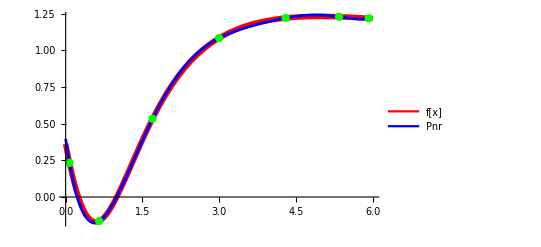

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

### в)

```mathematica
Intf=Interpolation[data];
```

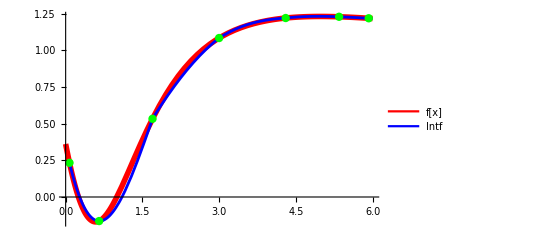

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

### г)

```mathematica
f[2.4316]
Pnr/.x->2.4316
Intf[2.4316]
```

0.920893

0.932527

0.890226

### д)

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.0350472,{x→0.}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},x]
```

{0.0792782,{x→1.22049}}

### n = 10

```mathematica
n=10;
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i];]
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
TableForm[data]
```

5.96946 | 1.21704
5.7289 | 1.22227
5.26725 | 1.22911
4.62192 | 1.22777
3.8452 | 1.19561
3. | 1.08345
2.1548 | 0.801904
1.37808 | 0.292926
0.732751 | -0.144311
0.271104 | -0.0214034
0.0305357 | 0.307409

### а)

```mathematica
findDividedDiff[dataX_,dataY_,first_,last_]:=If[first+1==last,(dataY[[last]]-dataY[[first]])/(dataX[[last]]-dataX[[first]]),(findDividedDiff[dataX,dataY,first+1,last]-findDividedDiff[dataX,dataY,first,last-1])/(dataX[[last]]-dataX[[first]])]
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=""]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=findDividedDiff[dataX,dataY,i+1,k+i+1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
TableForm[tab]
```

1.21704 | -0.021772 | -0.00991183 | 0.00397236 | -0.00122315 | 0.000336964 | -0.0000454203 | -0.0000588736 | 0.0000598419 | 7.94819×10^-6 | -0.0000278247
1.22227 | -0.0148118 | -0.0152648 | 0.00657066 | -0.00222375 | 0.000510227 | 0.000224891 | -0.000372248 | 0.0000145502 | 0.000173197 | 
1.22911 | 0.00208592 | -0.0276419 | 0.012639 | -0.00404735 | -0.000468235 | 0.0020847 | -0.00045166 | -0.00097239 |  | 
1.22777 | 0.0413941 | -0.0562977 | 0.0252362 | -0.0022263 | -0.00992129 | 0.00434126 | 0.00464047 |  |  | 
1.19561 | 0.132705 | -0.118558 | 0.032458 | 0.0363593 | -0.0288093 | -0.0169649 |  |  |  | 
1.08345 | 0.333115 | -0.198636 | -0.0807084 | 0.139326 | 0.0359061 |  |  |  |  | 
0.801904 | 0.655288 | -0.0156502 | -0.460916 | 0.0327046 |  |  |  |  |  | 
0.292926 | 0.677543 | 0.852576 | -0.530389 |  |  |  |  |  |  | 
-0.144311 | -0.266236 | 1.5673 |  |  |  |  |  |  |  | 
-0.0214034 | -1.36682 |  |  |  |  |  |  |  |  | 
0.307409 |  |  |  |  |  |  |  |  |  |

```mathematica
diffRes=Table[diff[i,k],{i,0,n},{k,1,n}];
```

### б)

```mathematica
findNewtonDividedDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=findNewtonDividedDiff[dataX,dataY,n,diffRes]//Simplify
```

0.360467-1.7677 x+0.923946 x^2+2.13483 x^3-2.81903 x^4+1.59703 x^5-0.524709 x^6+0.106654 x^7-0.0132566 x^8+0.000925314 x^9-0.0000278247 x^10

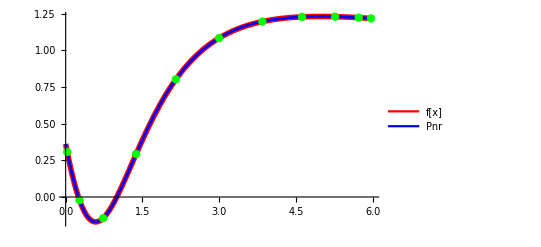

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

### в)

```mathematica
Intf=Interpolation[data];
```

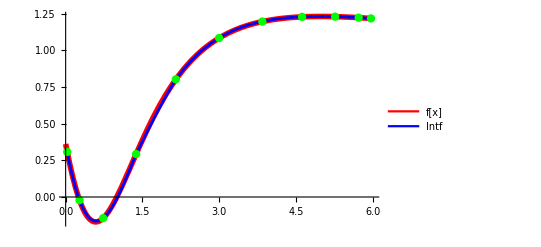

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

### г)

```mathematica
f[2.4316]
Pnr/.x->2.4316
Intf[2.4316]
```

0.920893

0.919821

0.919982

### д)

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.00122078,{x→2.56448}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},x]
```

{0.0168223,{x→1.74388}}

## Задание 3

По результатам 1 и 2 задания видно, что погрешность интерполирования зависит от числа узлов/степени многочлена (чем выше количество узлов, тем выше точность) и от расположения на отрезке (погрешность интерполирования многочленом степени n будет минимальной при использовании чебышевских узлов интерполяции по сравнению с равноотстоящими).

## Задание 4

```mathematica
n=10;
h=b/n;
data=N[Table[{i h,f[i h]},{i,0,n}]];
TableForm[data]
```

0. | 0.361389
0.6 | -0.169493
1.2 | 0.150834
1.8 | 0.601076
2.4 | 0.908823
3. | 1.08345
3.6 | 1.17407
4.2 | 1.2159
4.8 | 1.2298
5.4 | 1.22766
6. | 1.21631

### б)

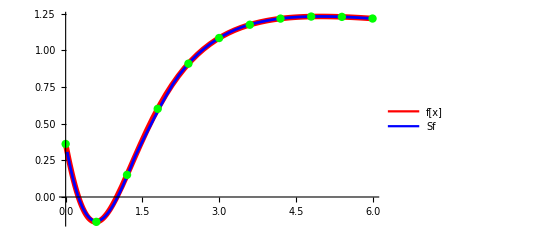

```mathematica
Sf=Interpolation[data,Method->"Spline"];
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Sf"}]]
```

### г)

```mathematica
f[2.4316]
Sf[2.4316]
```

0.920893

0.920876

## Задание 5

```mathematica
n=10;
b=6;
h=b/n;
data=N[Table[{i h,f[i h]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
TableForm[data]
```

0. | 0.361389
0.6 | -0.169493
1.2 | 0.150834
1.8 | 0.601076
2.4 | 0.908823
3. | 1.08345
3.6 | 1.17407
4.2 | 1.2159
4.8 | 1.2298
5.4 | 1.22766
6. | 1.21631

### а)

0.154756+0.221137 x

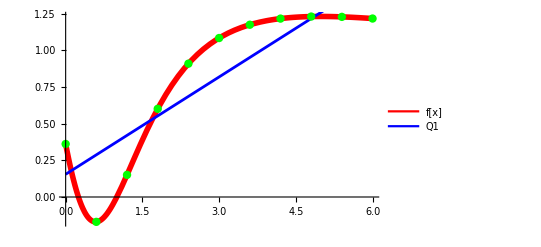

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,1}]];
polRes=0;
For[i=0,i<=1,i++,polRes=polRes+res[[i+1]]*x^i];
Q1=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q1,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q1"}]]
```

### б)

-0.0523877+0.451296 x-0.0383599 x^2

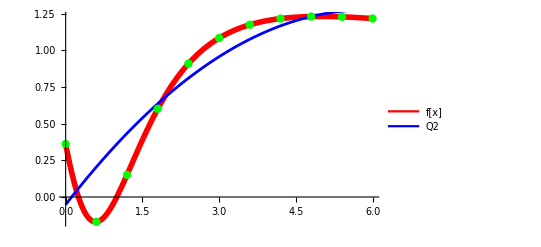

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,2}]];
polRes=0;
For[i=0,i<=2,i++,polRes=polRes+res[[i+1]]*x^i];
Q2=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q2,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q2"}]]
```

### в)

0.117733+0.000792759 x+0.158538 x^2-0.0218776 x^3

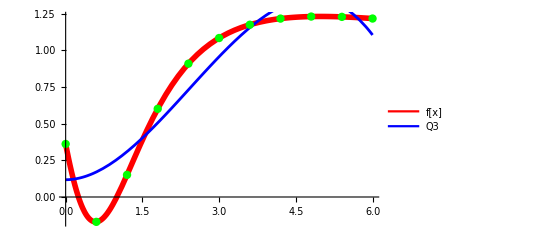

```mathematica
Q3=Fit[data,{1,x,x^2,x^3},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q3,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q3"}]]
```

0.282389-0.952083 x+0.952601 x^2-0.233628 x^3+0.0176458 x^4

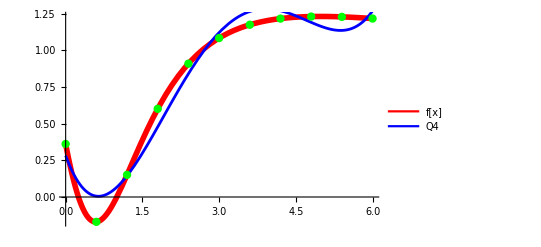

```mathematica
Q4=Fit[data,{1,x,x^2,x^3,x^4},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q4,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q4"}]]
```

### д)

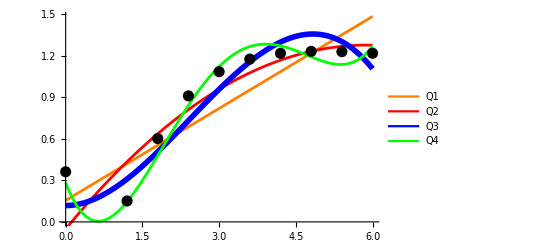

```mathematica
graph1=Plot[Q1,{x,a,b},PlotStyle->Orange];
graph2=Plot[Q2,{x,a,b},PlotStyle->Red];
graph3=Plot[Q3,{x,a,b},PlotStyle->{Blue,Thickness[0.01]}];
graph4=Plot[Q4,{x,a,b},PlotStyle->Green];
graph5=ListPlot[data,PlotStyle->{PointSize[0.02],Black}];
Legended[Show[graph1,graph2,graph3,graph4,graph5],LineLegend[{Orange,Red,Blue,Green},{"Q1","Q2","Q3","Q4"}]]
```